### Wprowadzenie wartości dla temperatury wody ( "T_2" ), masy ( "m" ) i ciepła właściwego żelaza ( "c" ).

```mathematica
ClearAll["Global`*"];

T2=291;    (* K *)
c=470;       (* J/(kg K)*)
```

### Obliczenie ciepła ( "ΔQ" ) wymienionego pomiędzy żelazem a woda.

```mathematica
ΔQ=m×c×(T1-T2);
```

### Obliczenie przyrostu entropii żelaza ( "ΔS_1" ) i wody ( "ΔS_2" ).

```mathematica
ΔS1=∫_T1^T2 m×c ⅆT/T;
ΔS2=ΔQ/T2;
```

### Sporządzenie wykresu obrazującego zależność przyrostu entropii żelaza od jego temperatury początkowej.

```mathematica
rys1=Plot[ΔS1/.m->100,{T1,373,523},PlotStyle->{Black,Thickness[0.006]}];
rys2=Plot[ΔS1/.m->150,{T1,373,523},PlotStyle->{Gray,Thickness[0.006]}];
```

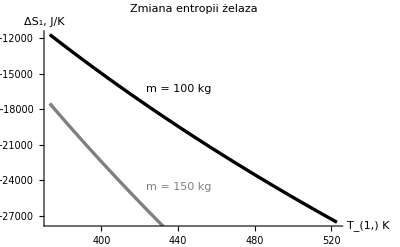

```mathematica
rys3=Show[rys1,rys2,
BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},
PlotLabel->StyleForm["       Zmiana entropii żelaza",
FontFamily->"Helvetica",
FontSlant->"Plain",
FontWeight ->"Bold",
FontSize->12],
AxesLabel->{"T_(1,) K ","ΔS_1, J/K"},
Prolog->{Text[StyleForm["m = 100 kg",FontColor->Black],Scaled[{0.45,0.7}]],
Text[StyleForm["m = 150 kg ",FontColor->Gray],Scaled[{0.45,0.20}]]}]
```

### Sporządzenie wykresu obrazującego zależność przyrostu entropii wody od temperatury początkowej żelaza.

```mathematica
rys4=Plot[ΔS2/.m->100,{T1,373,523},PlotStyle->{Black,Thickness[0.006]}];
rys5=Plot[ΔS2/.m->150,{T1,373,523},PlotStyle->{Gray,Thickness[0.006]}];
```

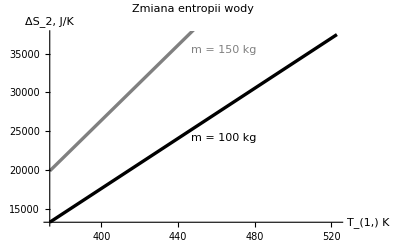

```mathematica
rys6=Show[rys4,rys5,
BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},
PlotLabel->StyleForm["       Zmiana entropii wody",
FontFamily->"Helvetica",
FontSlant->"Plain",
FontWeight ->"Bold",
FontSize->12],
AxesLabel->{"T_(1,) K ","ΔS_2, J/K"},
Prolog->{Text[StyleForm["m = 100 kg",FontColor->Black],Scaled[{0.6,0.45}]],
Text[StyleForm["m = 150 kg ",FontColor->Gray],Scaled[{0.6,0.90}]]}]
```

```mathematica
rys7=Plot[ΔS2+ΔS1/.m->100,{T1,373,523},PlotStyle->{Black,Thickness[0.006]}];
rys8=Plot[ΔS2+ΔS1/.m->150,{T1,373,523},PlotStyle->{Gray,Thickness[0.006]}];
```

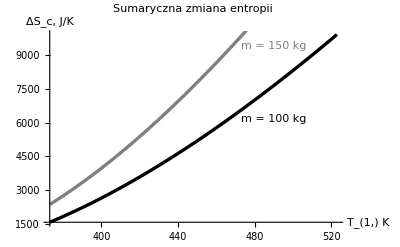

```mathematica
rys9=Show[rys7,rys8,
BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},
PlotLabel->StyleForm["      Sumaryczna zmiana entropii",
FontFamily->"Helvetica",
FontSlant->"Plain",
FontWeight ->"Bold",
FontSize->12],
AxesLabel->{"T_(1,) K ","ΔS_c, J/K"},
Prolog->{Text[StyleForm["m = 100 kg",FontColor->Black],Scaled[{0.77,0.55}]],
Text[StyleForm["m = 150 kg ",FontColor->Gray],Scaled[{0.77,0.92}]]}]
```